{{x→InterpolatingFunction[{{0., 1.867}}, <>],y→InterpolatingFunction[{{0., 1.867}}, <>],ψ→InterpolatingFunction[{{0., 1.867}}, <>],e_y→InterpolatingFunction[{{0., 1.867}}, <>],e_ψ→InterpolatingFunction[{{0., 1.867}}, <>]}}

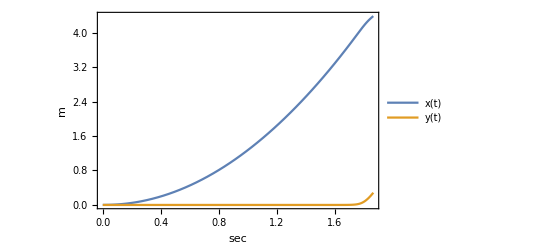

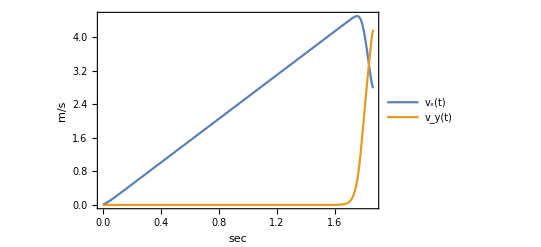

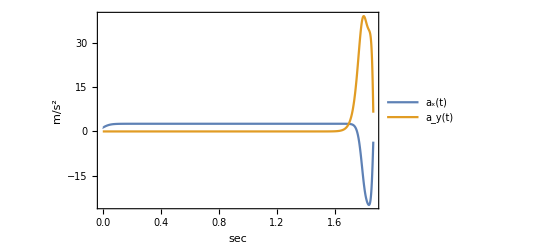

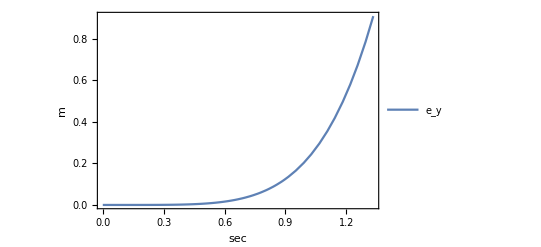

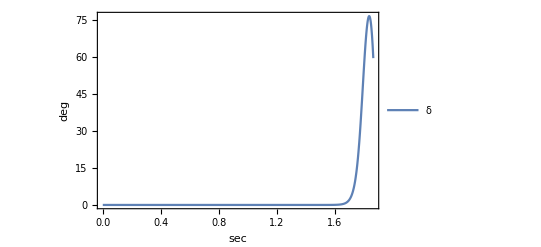

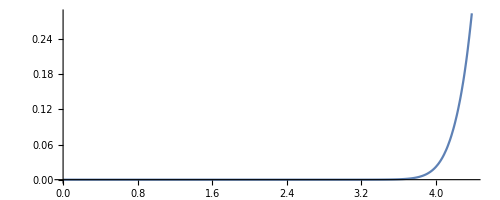

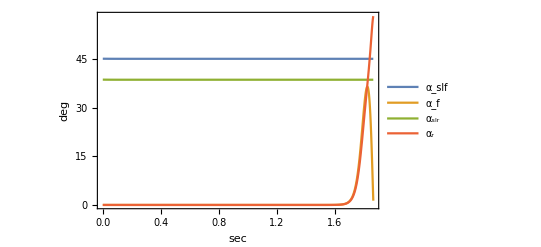

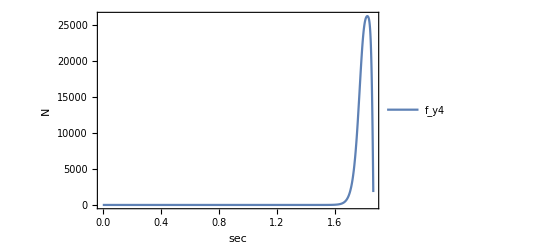

```mathematica
Ratio1[βr_]:=√(1.0-βr^2);
Brake1[t_,τ_,βr_]:=βr/2*(Tanh[20t]-Tanh[20(t-τ)]);
Brake[t_,τ0_,τ_,βr_]:=Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]];
S1[t_,τ1_,δ1_]:=δ1/2*(Tanh[20t]-Tanh[20(t-τ1)]);
S2[t_,τ01_,τ1_,δ1_]:=Fold[Plus,0,Table[S1[t-τ01⟦k⟧,τ1⟦k⟧,δ1⟦k⟧],{k,1,Length[τ1]}]];
η = Ratio1[(Brake[t,τ0 ,τ ,Subscript[β, r]])];
δ = S2[t,τ01,τ1,δ1];

Slip angle;
f[μ_,F_,C_]:=ArcTan[(3η μ F)/C]/.rules;
Subscript[α, sl1]=f[Subscript[μ, 1],Subscript[F, z1],Subscript[C, α1]]; Subscript[α, sl2]=f[Subscript[μ, 2],Subscript[F, z2],Subscript[C, α2]];
Subscript[α, sl3]=f[Subscript[μ, 3],Subscript[F, z3],Subscript[C, α3]]; Subscript[α, sl4]=f[Subscript[μ, 4],Subscript[F, z4],Subscript[C, α4]];

f[δ_,l_]:=(y'[t] + l ψ'[t])/x'[t]-δ/.rules;
Subscript[α, 1]=f[δ,Subscript[l, f]]; Subscript[α, 2]=f[δ,Subscript[l, f]];
Subscript[α, 3]=f[0,Subscript[l, r]]; Subscript[α, 4]=f[0,Subscript[l, r]];

Tire  Force;
f[C_,α_,μ_,F_,αs_]:=Piecewise[{{ - C Tan[α]+ C^2/(3η μ F) Abs[Tan[α]] Tan[α]- C^3/(27(η μ F)^2)Tan[α]^3,Abs[α]<αs},{-η μ F Sign[α],Abs[α]≥αs}}]/.rules;
Subscript[f, y1]=f[Subscript[C, α1],Subscript[α, 1],Subscript[μ, 1],Subscript[F, z1],Subscript[α, sl1]]/.rules; Subscript[f, y2]=f[Subscript[C, α2],Subscript[α, 2],Subscript[μ, 2],Subscript[F, z2],Subscript[α, sl2]]/.rules;
Subscript[f, y3]=f[Subscript[C, α3],Subscript[α, 3],Subscript[μ, 3],Subscript[F, z3],Subscript[α, sl3]]/.rules; Subscript[f, y4]=f[Subscript[C, α4],Subscript[α, 4],Subscript[μ, 4],Subscript[F, z4],Subscript[α, sl4]]/.rules;

f[μ_,F_]:=Brake[t,τ0,τ,Subscript[β, r]]  μ F/.rules;
Subscript[f, x1]=f[Subscript[μ, 1],Subscript[F, z1]]/.rules; Subscript[f, x2]=f[Subscript[μ, 2],Subscript[F, z2]]/.rules;
Subscript[f, x3]=f[Subscript[μ, 3],Subscript[F, z3]]/.rules; Subscript[f, x4]=f[Subscript[μ, 4],Subscript[F, z4]]/.rules;

Subscript[F, x1] =Subscript[f, x1] Cos[δ] - Subscript[f, y1] Sin[δ]; Subscript[F, x2] =Subscript[f, x1] Cos[δ] - Subscript[f, y1] Sin[δ];
Subscript[F, x3] =Subscript[f, x1] Cos[0] - Subscript[f, y1] Sin[0]; Subscript[F, x4] =Subscript[f, x1] Cos[0] - Subscript[f, y1] Sin[0];

Subscript[F, y1] =Subscript[f, x1] Sin[δ] + Subscript[f, y1] Cos[δ]; Subscript[F, y2] =Subscript[f, x1] Sin[δ] + Subscript[f, y1] Cos[δ];
Subscript[F, y3] =Subscript[f, x1] Sin[0] + Subscript[f, y1] Cos[0]; Subscript[F, y4] =Subscript[f, x1] Sin[0] + Subscript[f, y1] Cos[0];

Eq1 = m x''[t]== m y'[t]ψ'[t] + Subscript[F, x1] +Subscript[F, x2] +Subscript[F, x3] +Subscript[F, x4]/.rules;
Eq2 = m y''[t] == -m x'[t] ψ'[t] + Subscript[F, y1]+ Subscript[F, y2]+ Subscript[F, y3]+ Subscript[F, y4]/.rules;
Eq3 =Subscript[J, z] ψ''[t] == Subscript[l, f](Subscript[F, y1] + Subscript[F, y2]) - Subscript[l, r](Subscript[F, y3] + Subscript[F, y4]) + (Subscript[ω, t]/2)( Subscript[F, x2] -Subscript[F, x1] - Subscript[F, x3] + Subscript[F, x4])/.rules;
Eq4 = m Subscript[e, ψ]'[t]==m  ψ'[t]-m D[Subscript[ψ, d][t],t]/.rules;
Eq5 = m Subscript[e, y]'[t]==m y'[t] Cos[Subscript[e, ψ][t]] + m x'[t]Sin[Subscript[e, ψ][t]]/.rules;

Subscript[ψ, d][t]=ArcCos[x[t]^2/(Subscript[t, lp]  √(x'[t]^2+y'[t]^2))]/.rules;

rules =
{
Subscript[C, α1]->80000.0,Subscript[C, α2]->80000.0,Subscript[C, α3]->80000.0,Subscript[C, α4]->80000.0,
Subscript[μ, 1]->1.0,Subscript[μ, 2]->1.0,Subscript[μ, 3]->1.0,Subscript[μ, 4]->1.0,
Subscript[F, z1]->26719.0,Subscript[F, z2]->26719.0,Subscript[F, z3]->21295.0,Subscript[F, z4]->21295.0(*NOT SURE*),
m ->2050.0,Subscript[ω, t]->1.63,Subscript[l, f]->1.43,Subscript[l, r]->1.47 , Subscript[J, z] -> 3344.0 ,
Subscript[K, y]->0,Subscript[K, ψ]-> 0,Subscript[ψ, d1] ->-0.12,Subscript[t, lp] -> 1.5
};

time =1.867;

τ0 = {0,10,20,50};
τ = {2,5,5,5};
Subscript[β, r]={0.05,0.5,-0.5,0.6};

τ01 = {1.8,1.9,19,102,135 ,140};
τ1 = {0.1,0.1,39,4,3 ,20};
δ1={2,-2,0.025,0.02,-0.025,0.025};

initCond={x[0]==0.001,x'[0]==0.01,y[0]==0,y'[0]==0,ψ[0]==0,ψ'[0]==0,Subscript[e, y][0]==0,Subscript[e, ψ][0]==0};

solution=NDSolve[{Eq1,Eq2,Eq3,Eq4,Eq5,initCond},{x,y,ψ,Subscript[e, y],Subscript[e, ψ]},{t,0,time}]

Plot[Evaluate[{x[t],y[t]}/.solution],{t,0,time},Frame->True,FrameLabel->{"sec","m"},PlotLegends->{"x(t)","y(t)"},PlotRange->All] 
Plot[Evaluate[{x'[t],y'[t]}/.solution],{t,0,time},Frame->True,FrameLabel->{"sec","m/s"},PlotLegends->{"v_x(t)","v_y(t)"},PlotRange->All] 
Plot[Evaluate[{x''[t],y''[t]}/.solution],{t,0,time},Frame->True,FrameLabel->{"sec","m/s^2"},PlotLegends->{"a_x(t)","a_y(t)"},PlotRange->All] 
Plot[Evaluate[{Subscript[e, y][t]}/.solution],{t,0,time},Frame->True,FrameLabel->{"sec","m"},PlotLegends->{"e_y"},PlotRange->All] 
Plot[Evaluate[{δ*180/π}/.solution],{t,0,time},Frame->True,FrameLabel->{"sec","deg"},PlotLegends->{"δ"},PlotRange->All]
ParametricPlot[Evaluate[{x[t],y[t]}/.solution],{t,0,time},PlotRange-> All]
Plot[Evaluate[{Subscript[α, sl1]*180/π,Abs[Subscript[α, 1]]*180/π,Subscript[α, sl3]*180/π,Abs[Subscript[α, 3]]*180/π}/.solution],{t,0,time},Frame->True,FrameLabel->{"sec","deg"},PlotLegends->{"α_slf","α_f","α_slr","α_r"},PlotRange->All]
Plot[Evaluate[{Subscript[f, y1]}/.solution],{t,0,time},Frame->True,FrameLabel->{"sec","N"},PlotLegends->{"f_y4"},PlotRange->All]
```